```mathematica
PolLagr[A_,f_]:=Module[{i,j,n,Pol=0},
n=Length[A];
For[i=1,i≤n,i++,
L=1;
For[j=1,j≤n,j++,
If[j≠i,
L=L*(x-A[[j]])/(A[[i]]-A[[j]])];
];
Pol=Pol+L*f[A[[i]]];
];
Print["El polinomio de Lagrange que pasa por los puntos ",A, "corresponde a ",Simplify[Pol], "con gráfica: "];
PolinomioLagrange:=Simplify[Pol];
Plot[{f[x],PolinomioLagrange},{x,A[[1]]-1,A[[n]]+1},PlotLegends->"Expressions"]

];
```

```mathematica
A={0,1,2};
f[x_]:=ⅇ^x;
```

El polinomio de Lagrange que pasa por los puntos {0,1,2}corresponde a 1/2 (2-(3-4 ⅇ+ⅇ^2) x+(-1+ⅇ)^2 x^2)con gráfica:

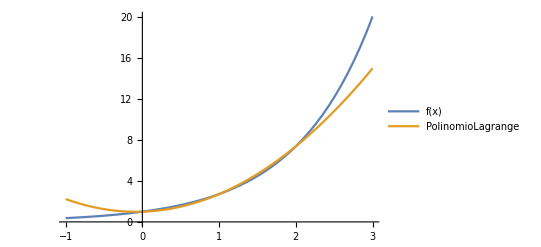

```mathematica
PolLagr[A,f]
```